```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
<<"HeterogeneousTemplate.wl";

GenerateMarkovTemplates[  MarkovProc_, NumTemplates_, LenTemplates_ ] :=
	(RandomFunction[MarkovProc,{#,LenTemplates}][[2]][[1]][[1]])&/@ConstantArray[1,NumTemplates];

(*The small kbind limit, should result in purely Energetic Discrimination*)
(*output order is kbind, M, gbb, Meff, kpol, ktb*)
SmallkbindLimit[gpo_,copysize_,templatesize_,kineticFactor_] :=
	{Exp[kineticFactor]*ConstantArray[1,{copysize, templatesize}],Exp[-kineticFactor]*ConstantArray[1,copysize],gpo+kineticFactor,{{1,1},{1,1}},
	Exp[kineticFactor]*ConstantArray[1,{copysize,templatesize,copysize,templatesize}],
	Exp[kineticFactor]*ConstantArray[1,{copysize,templatesize}],kineticFactor}

RandomMarkovVel[  inputtemplate_,gpo_,EnergyMatrix_,KineticMatrix_ ] :=  Module[ {ErrorProbs, param, kbind, M,gbb, Meff, kpol, ktb,
		coarse, Probs, temp, copysize, templatesize, ProbsUnnormed, 
		AllOutput,visitationMatrixls,Lengthtimes,Ggen},
	copysize = 2;
	templatesize = 2;
	
	param =SmallkbindLimit[gpo,copysize,templatesize,12];
	
	kbind = param[[1]];
	M = param[[2]]; 
	gbb= param[[3]];
	Meff = param[[4]];
	kpol = param[[5]];
	ktb =  param[[6]];
	Ggen = param[[7]];
	
	coarse = GetProbabilityTensor[gpo,EnergyMatrix,KineticMatrix,
		copysize,templatesize,kbind,M,Ggen];
	
	Probs = GetProbabilityTensorFine[gbb,EnergyMatrix,kbind,ktb,
		kpol,M,Meff,Ggen,copysize,templatesize];
	temp = GetKineticTensors[gbb,EnergyMatrix,kbind,ktb,kpol,M,
		Meff,Ggen,copysize,templatesize];
	ProbsUnnormed = GetUnnormedProbabilityTensor[gbb,EnergyMatrix,
		kbind,ktb,kpol,M,Meff,Ggen,copysize,templatesize];
	
	AllOutput = GetTransferMatrixList[gpo,EnergyMatrix,KineticMatrix,
		inputtemplate,kbind,M,Ggen];
	visitationMatrixls = GetVisitationList[AllOutput[[2]]][[1]];
			
	Lengthtimes =GetTimes[ visitationMatrixls, gpo,temp,copysize,
		templatesize,inputtemplate][[2]];
	
	Return[Length[inputtemplate]/Total[Lengthtimes]];
 ]
```

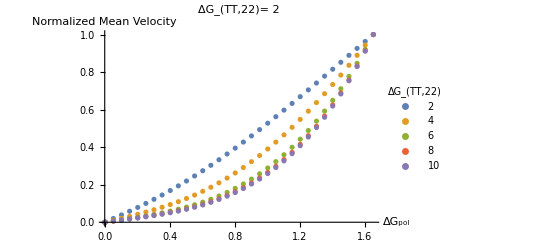

```mathematica
KineticMatrix =  {{0,0},{0,0}};
velData= {};
Raw = {};
Get["masterTemplate"];
inputtemplate = masterTemplate;
Domain = Insert[Range[-0.69,1.0,0.05],-Log[2],1];
For [ x = 2.0,x<=10.1,x = x+2.0,
	EnergyMatrix={{2.0,0},{0,x}};
	MeanVel =RandomMarkovVel[  inputtemplate,#,EnergyMatrix,KineticMatrix] &/@ Domain;
	NormVel= MeanVel/Last[MeanVel];
	velData =Append[velData,Transpose@{Domain+Log[2],NormVel}];
	Raw =Append[Raw,Transpose@{Domain+Log[2],MeanVel}];
]

mu={2,4,6,8,10};
pl=PointLegend[mu,LegendLabel->Subscript["ΔG","TT,22"],LegendFunction->"Frame",LegendLayout->Automatic,LegendMarkers->Automatic];
p1 =ListPlot[velData,AxesLabel->{Subscript["ΔG","pol"],"Normalized Mean Velocity"},
		PlotLegends->Placed[pl,Right],PlotLabel->Row[{Subscript["ΔG","TT,22"],"= 2"}]]
```

```mathematica
Save["TempTherm.NormalizedVelocityData",velData]
Save["TempTherm.RawVelocityData",Raw]
```

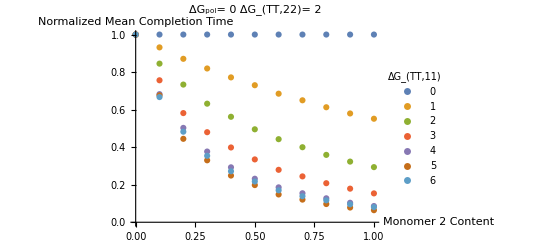

```mathematica
KineticMatrix =  {{0,0},{0,0}};
gpo = 0.0;

PreDomain =  Range[0,1,0.1];
ErrorData= {};
Raw = {};
Domain = {1-#,#} &/@PreDomain;

For [ x = 0.0,x<=6.1,x = x+1.0,
	EnergyMatrix =  {{6.0,x},{0,6.0}};
	MeanErrors =RandomMarkovTime[  2,#,10000,gpo,EnergyMatrix,KineticMatrix] &/@Domain;
	times = MeanErrors/Max[MeanErrors[[1]],Last[MeanErrors]];
	ErrorData =Append[ErrorData,Transpose@{PreDomain,times}];
	Raw =Append[Raw,Transpose@{PreDomain,MeanErrors}];
]

mu={0,1,2,3,4,5,6};
pl=PointLegend[mu,LegendLabel->Subscript["ΔG","TT,11"],LegendFunction->"Frame",LegendLayout->Automatic,LegendMarkers->Automatic];
p1 =ListPlot[ErrorData,AxesLabel->{"Monomer 2 Content","Normalized Mean Completion Time"},
		PlotLegends->Placed[pl,Right],PlotLabel->Row[{Subscript["ΔG","pol"],"= 0    ",
		Subscript["ΔG","TT,22"],"= 2"}]]
```

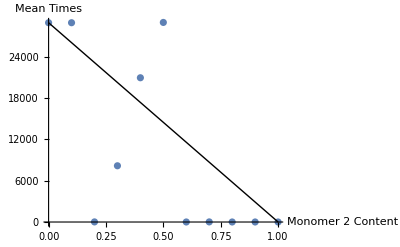

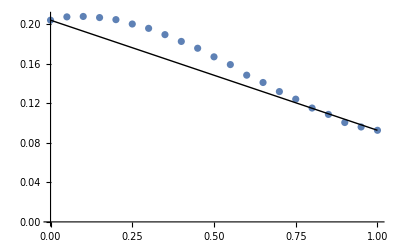

```mathematica
data1 = Raw[[6]];
p1 =ListPlot[data1,AxesLabel->{"Monomer 2 Content","Mean Times"}];
p2 = Graphics[Line[{data1[[1]],data1[[-1]]}]];
Show[{p1,p2}]
```

```mathematica
Save["Normalized",ErrorData]
Save["Unnormalized",Raw]
```

```mathematica
Max[1,2]
```

2

```mathematica
Raw[[5]]
```

{{0.,513.798},{0.1,371.805},{0.2,145.836},{0.3,2.04904},{0.4,371.805},{0.5,2.07269},{0.6,2.00812},{0.7,0.623222},{0.8,3.47735},{0.9,0.623222},{1.,0.623222}}

```mathematica
A =RandomMarkovTime[  2,#,10000,gpo,{{2,0},{0,10}},{{0,0},{0,0}}] &/@Domain
```

{18.3189,1.06041×10^6,4.26102×10^6,9.16401×10^6,1.65808×10^7,2.39577×10^7,3.1183×10^7,3.85206×10^7,4.30053×10^7,4.06778×10^7,5.46657×10^6}

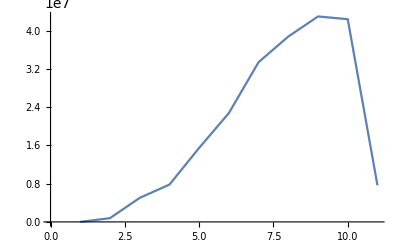

```mathematica
ListLinePlot[{18.35395563888888,783779.0198124667,5.0257612626797715*^6,7.7980114449028615*^6,1.5479817935539082*^7,2.276936415142884*^7,3.342045807227078*^7,3.877920194749455*^7,4.2983133707566366*^7,4.2411030454278715*^7,7.659289304499788*^6}]
```

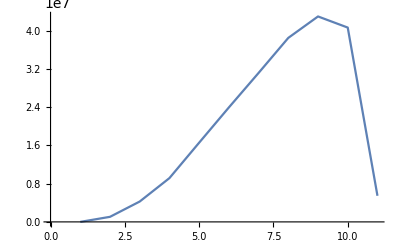

```mathematica
ListLinePlot[A]
```

```mathematica
PreDomain
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

```mathematica
MeanVel
```

MeanVel